```mathematica
SetOptions[SelectedNotebook[],FontProperties->{"ScreenResolution"->Automatic}];
```

```mathematica
Quit[];
```

```mathematica
SetDirectory@NotebookDirectory[];
<<"Include.m";
Include/@{"Def.nb"};
```

### Single Ion

#### 2 Level - Pauli

```mathematica
ϕ=.;
H=({{0, Ω/2 ⅇ^(ⅈ (Δ t+ϕ))}, {Ω/2 ⅇ^(-ⅈ (Δ t+ϕ)), 0}})/.{Ω->1,Δ->0};
H//MatrixForm
ⅈ MatrixExp[-ⅈ H t]/.{t->π,ϕ->0}//MatrixForm
-ⅈ MatrixExp[-ⅈ H t]/.{t->π,ϕ->π/2}//MatrixForm
```

(0 | ⅇ^(ⅈ ϕ)/2
ⅇ^(-ⅈ ϕ)/2 | 0)

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

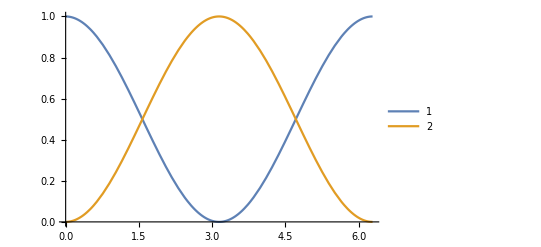

```mathematica
ϕ=0;
T=2π;
func=Function@@{t,MatrixExp[-ⅈ H t].{1,0}};f[x_?NumberQ,i_]:=func[x]⟦i⟧;
Plot[Evaluate[Abs[f[t,#]]^2&/@Range[2]],{t,0,T},PlotLegends->Automatic]
```

```mathematica
H=({{0, Ω/2 ⅇ^(ⅈ (Δ t+ϕ))}, {Ω/2 ⅇ^(-ⅈ (Δ t+ϕ)), 0}})/.{Ω->1,Δ->10,ϕ->0};
H//MatrixForm
```

(0 | 1/2 ⅇ^(10 ⅈ t)
1/2 ⅇ^(-10 ⅈ t) | 0)

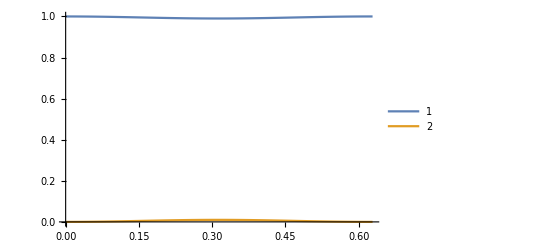

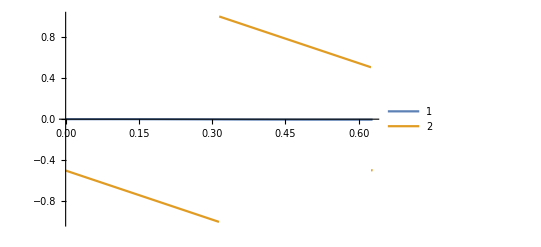

```mathematica
T=2π/10;
func=NDSolveValue[{ⅈ D[ψ[t], t]==H.ψ[t],ψ[0]=={1,0}},ψ[t],{t,0,T}]⟦0⟧;
f[x_?NumberQ,i_]:=func[x]⟦i⟧;
Plot[Evaluate[Abs[f[t,#]]^2&/@Range[2]],{t,0,T},PlotLegends->Automatic]
Plot[Evaluate[Arg[f[t,#]]/π&/@Range[2]],{t,0,T},PlotLegends->Automatic]
```

```mathematica
H=EffectiveHamiltonian@H;
H//MatrixForm
```

(1/40 | 0
0 | -1/40)

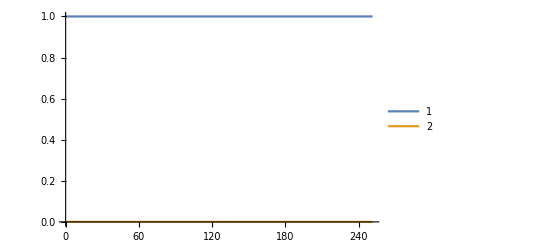

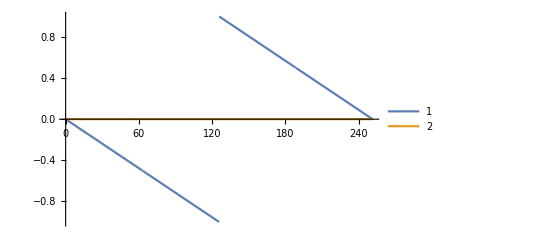

```mathematica
T=40 2π;
func=Function@@{t,MatrixExp[-ⅈ H t].{1,0}};f[x_?NumberQ,i_]:=func[x]⟦i⟧;
Plot[Evaluate[Abs[f[t,#]]^2&/@Range[2]],{t,0,T},PlotLegends->Automatic]
Plot[Evaluate[Arg[f[t,#]]/π&/@Range[2]],{t,0,T},PlotLegends->Automatic]
```

```mathematica
MatrixExp[ⅈ (π/2)/2 PauliMatrix[2]].PauliMatrix[1].MatrixExp[-ⅈ (π/2)/2 PauliMatrix[2]]==PauliMatrix[3]
```

True

```mathematica
TrigToExp[MatrixExp[ⅈ (π/2)/2 PauliMatrix[2]].MatrixExp[-ⅈ θ/2 PauliMatrix[1]].MatrixExp[-ⅈ (π/2)/2 PauliMatrix[2]]]==MatrixExp[-ⅈ θ/2 PauliMatrix[3]]
```

True

#### 3 Level - Raman

```mathematica
H0=({{0, 0, 0}, {0, 100, 0}, {0, 0, 200}});
H1=({{0, 1/2 ⅇ^(ⅈ t ν1) Ω1, 1/2 ⅇ^(ⅈ t ν1) Ω1}, {1/2 ⅇ^(-ⅈ t ν1) Ω1, 0, 0}, {1/2 ⅇ^(-ⅈ t ν1) Ω1, 0, 0}});
H2=({{0, 1/2 ⅇ^(ⅈ t ν2) Ω2, 1/2 ⅇ^(ⅈ t ν2) Ω2}, {1/2 ⅇ^(-ⅈ t ν2) Ω2, 0, 0}, {1/2 ⅇ^(-ⅈ t ν2) Ω2, 0, 0}});
T=40π;
H=Expand[MatrixExp[ⅈ H0 t].(H1+H2).MatrixExp[-ⅈ H0 t]/.{Ω1->1,Ω2->1,ν1->110,ν2->210}];
H//MatrixForm
```

(0 | 1/2 ⅇ^(10 ⅈ t)+1/2 ⅇ^(110 ⅈ t) | 1/2 ⅇ^(10 ⅈ t)+1/2 ⅇ^(-90 ⅈ t)
1/2 ⅇ^(-10 ⅈ t)+1/2 ⅇ^(-110 ⅈ t) | 0 | 0
1/2 ⅇ^(-10 ⅈ t)+1/2 ⅇ^(90 ⅈ t) | 0 | 0)

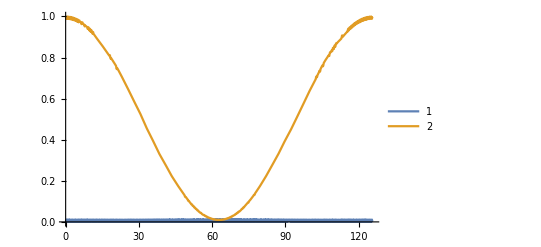

```mathematica
func=NDSolveValue[{ⅈ D[ψ[t], t]==H.ψ[t],ψ[0]=={0,1,0}},ψ[t],{t,0,T}]⟦0⟧;
f[x_?NumberQ,i_]:=func[x]⟦i⟧;
Plot[Evaluate[Abs[f[t,#]]^2&/@Range[2]],{t,0,T},PlotLegends->Automatic]
```

```mathematica
H=EffectiveHamiltonian@H;
H//MatrixForm
H=RotatingWaveApproximation[Normal@H,99];
H//MatrixForm
```

(49/990+(49 ⅇ^(-100 ⅈ t))/1980+(49 ⅇ^(100 ⅈ t))/1980 | 0 | 0
0 | -3/110-3/220 ⅇ^(-100 ⅈ t)-3/220 ⅇ^(100 ⅈ t) | -1/40-(49 ⅇ^(-100 ⅈ t))/1980+ⅇ^(-200 ⅈ t)/3960
0 | -1/40-(49 ⅇ^(100 ⅈ t))/1980+ⅇ^(200 ⅈ t)/3960 | -1/45-1/90 ⅇ^(-100 ⅈ t)-1/90 ⅇ^(100 ⅈ t))

(49/990 | 0 | 0
0 | -3/110 | -1/40
0 | -1/40 | -1/45)

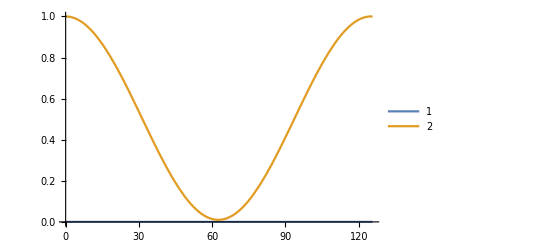

```mathematica
func=Function@@{t,MatrixExp[-ⅈ H t].{0,1,0}};f[x_?NumberQ,i_]:=func[x]⟦i⟧;
Plot[Evaluate[Abs[f[t,#]]^2&/@Range[2]],{t,0,T},PlotLegends->Automatic]
```

#### AC Stark Shift

```mathematica
SetPrecision[(Eigenvalues[({{0, Subscript[Ω, 1]/2, Subscript[Ω, 2]/2}, {Subscript[Ω, 1]/2, Subscript[ω, 1]-ν, 0}, {Subscript[Ω, 2]/2, 0, Subscript[ω, 2]-ν}})]-{0,Subscript[ω, 1]-ν,Subscript[ω, 2]-ν})/.{ν->80.,Subscript[ω, 1]->100.,Subscript[ω, 2]->200.,Subscript[Ω, 1]->1.,Subscript[Ω, 2]->1.},7]
```

{-0.01457398,0.01249064,0.002083341}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{1.41421,1.4146},{2.23607,2.23237},{3.16228,3.17011},{4.12311,4.12789},{5.09902,5.08976},{6.08276,6.08852},{7.07107,7.06814},{8.06226,8.06816},{9.05539,9.04941},{10.0499,10.0471}}

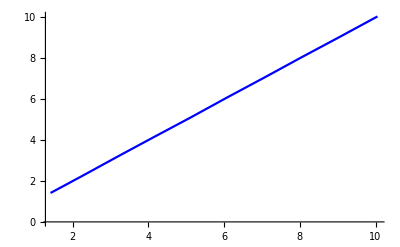

```mathematica
a=.;
ϕ=.;
Table[{N[√(1+λ^2)],Module[{f},f=(ψ[t]/.NDSolve[{ⅈ D[ψ[t], t]== Ω({{0, ⅇ^(ⅈ Δ t)}, {ⅇ^(-ⅈ Δ t), 0}}).ψ[t],ψ[0]=={1,0}}/.{Ω->2π,Δ->2λ π},ψ[t],{t,0,5}])[[1]];ω/(2π)/.FindFit[Table[Abs[f[[2]]]^2,{t,0,5,0.1}],a Sin[ω t+ϕ],{a,{ω,2 √(1+λ^2)π},ϕ},t]]},{λ,1,10}]
ListLinePlot[%,PlotRange->All,PlotStyle->{Red,Blue}]
```

#### Def

```mathematica
TrappedIon[{},{}];
```

```mathematica
ClearAll[Frequency,Strength];
Frequency@{args__}:=Frequency[args];
Strength@{args__}:=Strength[args];
Strength[__]=1;
```

(0 | 1.
1. | 0)

Piecewise[{{{{Cos[π #1],-ⅈ Sin[π #1]},{-ⅈ Sin[π #1],Cos[π #1]}}, 0≤#1≤1/2}, {0, True}}]&

(0 | 1
1 | 0)

(0 | 1
1 | 0)

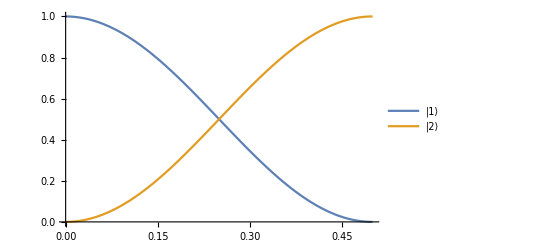

```mathematica
defs={{{1,2},{π,0}}};
Chop[ⅈ Evolution[Hamiltonian@defs,IdentityMatrix@FullDimension],1*^-6]//MatrixForm
EvolutionFunction[Hamiltonian@defs,IdentityMatrix@FullDimension,t,Method->Constant]
ⅈ %[1/2]//MatrixForm
ⅈ Rot@defs//MatrixForm
EvolutionPlot@Hamiltonian@defs
```

(0 | -ⅈ
ⅈ | 0)

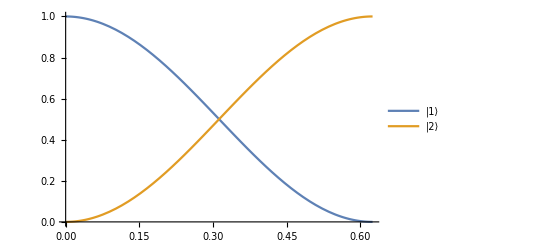

```mathematica
defs={{{1,2},{π,π/2}}};
ⅈ Rot@defs//MatrixForm
EvolutionPlot@Hamiltonian@defs
```

```mathematica
defs={{{1,2},{π/2,-π/2}},{{1,2},{θ,0}},{{1,2},{π/2,π/2}}};
Rot@defs//TrigToExp//MatrixForm
```

(ⅇ^((ⅈ θ)/2) | 0
0 | ⅇ^(-(ⅈ θ)/2))

```mathematica
TrappedIon[{1,3},{}];
```

```mathematica
defs={{{1,2},{π,0}},{{1,3},{θ,π/2}},{{1,2},{π,π}}};
Rot@defs==Rot@{{2,3},{θ,0}}
```

True

```mathematica
defs={{{1,2},{π,π}},{{1,3},{θ,0}},{{1,2},{π,0}}};
Rot@defs==Rot@{{2,3},{θ,π/2}}
```

True

```mathematica
defs={{{1,2},{π,-π/2}},{{1,3},{θ,ϕ}},{{1,2},{π,π/2}}};
Rot@defs==Rot@{{2,3},{θ,ϕ}}
```

True

```mathematica
T=.;
defs={{{{{1,2},{1,0,δ}},{{1,3},{1,0,δ}}},T}}/.δ->10;
-Rot@defs//MatrixForm
```

(-ⅇ^(-1/10 ⅈ π T) | 0 | 0
0 | -1/2-1/2 ⅇ^((ⅈ π T)/10) | 1/2-1/2 ⅇ^((ⅈ π T)/10)
0 | 1/2-1/2 ⅇ^((ⅈ π T)/10) | -1/2-1/2 ⅇ^((ⅈ π T)/10))

(0 | ⅇ^(20 ⅈ π t) π | ⅇ^(20 ⅈ π t) π
ⅇ^(-20 ⅈ π t) π | 0 | 0
ⅇ^(-20 ⅈ π t) π | 0 | 0)

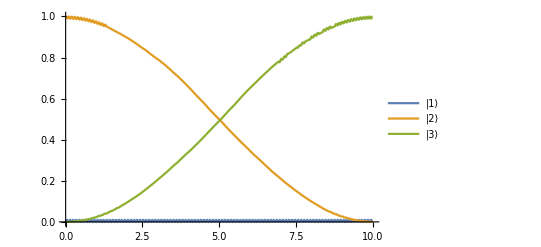

```mathematica
H=Hamiltonian[defs/.T->10];
H⟦1,1,1⟧//MatrixForm
EvolutionPlot[H,2]
```

(π/10 | 0 | 0
0 | -π/20 | -π/20
0 | -π/20 | -π/20)

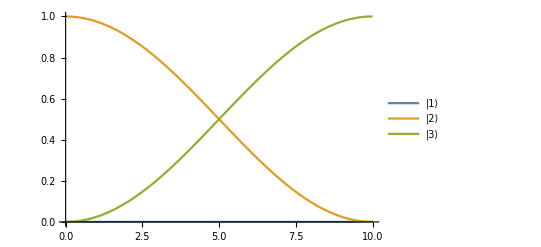

```mathematica
H=EffectiveHamiltonian@H;
H⟦1,1,1⟧//MatrixForm
EvolutionPlot[H,2,t,Method->Constant]
```

### Phonon

```mathematica
a=DiagonalMatrix[√Range[MDimension-1],1];
a//MatrixForm
a.UnitVector[MDimension,3]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{0,√2,0,0,0,0,0,0,0,0}

```mathematica
a†.a//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9)

### Cirac CNOT

```mathematica
TrappedIon[{1},{1},Dimensions-> {{g,Subscript[e, 0],Subscript[e, 1]},Range[0,2]}];
```

#### Controlled - Z

```mathematica
ClearAll[U];
U[k_,q_]:=MatrixExp[-ⅈ k π/2 Hermitian[KroneckerProduct[Subscript[e, q]@1 .g@1,PhononAnnihilation]]];
```

```mathematica
U[1,0].g,0==g,0
U[1,0].Subscript[e, 0],0==-ⅈ g,1
U[1,0].g,1==-ⅈ Subscript[e, 0],0
```

True

True

True

```mathematica
U[2,1].g,0==g,0
U[2,1].Subscript[e, 0],0==Subscript[e, 0],0
U[2,1].g,1==-g,1
U[2,1].Subscript[e, 0],1==Subscript[e, 0],1
```

True

True

True

«1 more identical outputs»

```mathematica
DimensionNumber⟦1⟧=2;
UpdateDimension[];
```

```mathematica
ClearAll[U];
U[1][k_,q_]:=MatrixExp[-ⅈ k π/2 Hermitian[KroneckerProduct[Subscript[e, q]@1 .g@1,NIdentity,PhononAnnihilation]]];
U[2][k_,q_]:=MatrixExp[-ⅈ k π/2 Hermitian[KroneckerProduct[NIdentity,Subscript[e, q]@1 .g@1,PhononAnnihilation]]];
```

```mathematica
U1=U[1][1,0];
U1.g,g,0==g,g,0
U1.g,Subscript[e, 0],0==g,Subscript[e, 0],0
U1.Subscript[e, 0],g,0==-ⅈ g,g,1
U1.Subscript[e, 0],Subscript[e, 0],0==-ⅈ g,Subscript[e, 0],1
```

True

True

True

«1 more identical outputs»

```mathematica
U2=U[2][2,1];
(U2.U1).g,g,0==g,g,0
(U2.U1).g,Subscript[e, 0],0==g,Subscript[e, 0],0
(U2.U1).Subscript[e, 0],g,0==ⅈ g,g,1
(U2.U1).Subscript[e, 0],Subscript[e, 0],0==-ⅈ g,Subscript[e, 0],1
```

True

True

True

«1 more identical outputs»

```mathematica
(U1.U1).g,g,0==g,g,0
(U1.U1).g,Subscript[e, 0],0==g,Subscript[e, 0],0
(U1.U1).Subscript[e, 0],g,0==-Subscript[e, 0],g,0
(U1.U1).Subscript[e, 0],Subscript[e, 0],0==-Subscript[e, 0],Subscript[e, 0],0
```

True

True

True

«1 more identical outputs»

#### 4π Spinor

```mathematica
(U1.U2.U1).g,g,0==g,g,0
(U1.U2.U1).g,Subscript[e, 0],0==g,Subscript[e, 0],0
(U1.U2.U1).Subscript[e, 0],g,0==Subscript[e, 0],g,0
(U1.U2.U1).Subscript[e, 0],Subscript[e, 0],0==-Subscript[e, 0],Subscript[e, 0],0
```

True

True

True

«1 more identical outputs»

```mathematica
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}).({{1}, {0}, {0}, {0}})//MatrixForm
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}).({{0}, {1}, {0}, {0}})//MatrixForm
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}).({{0}, {0}, {1}, {0}})//MatrixForm
({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}).({{0}, {0}, {0}, {1}})//MatrixForm
```

(1
0
0
0)

(0
1
0
0)

(0
0
1
0)

(0
0
0
-1)

#### Controlled - Z to Controlled - X

```mathematica
MatrixExp[-ⅈ π/4 PauliMatrix[2]].PauliMatrix[3].MatrixExp[ⅈ π/4 PauliMatrix[2]]==PauliMatrix[1]
```

True

```mathematica
ClearAll[V];
V[1][k_,ϕ_]:=MatrixExp[-ⅈ k π/2 Hermitian[KroneckerProduct[Subscript[e, 0]@1 .g@1 ⅇ^(-i ϕ),NIdentity,MIdentity]]];
V[2][k_,ϕ_]:=MatrixExp[-ⅈ k π/2 Hermitian[KroneckerProduct[NIdentity,Subscript[e, 0]@1 .g@1 ⅇ^(-ⅈ ϕ),MIdentity]]];
```

```mathematica
V1=V[2][1/2,π/2];
V2=V[2][1/2,-π/2];
V1.(U1.U2.U1).V2.g,g,0==g,g,0
V1.(U1.U2.U1).V2.g,Subscript[e, 0],0==g,Subscript[e, 0],0
V1.(U1.U2.U1).V2.Subscript[e, 0],g,0==-Subscript[e, 0],Subscript[e, 0],0
V1.(U1.U2.U1).V2.Subscript[e, 0],Subscript[e, 0],0==-Subscript[e, 0],g,0
```

True

True

True

«1 more identical outputs»

#### Def

```mathematica
TrappedIon[{2,3},{1,3}];
```

```mathematica
defs={{{1,{1,2,-1}},{π,0}},{{2,{1,3,-1}},{2π,0}},{{1,{1,2,-1}},{π,0}}};
H=Hamiltonian@defs;
Chop[Evolution[H,1,1,0]-1,1,0,1*^-6]
Chop[Evolution[H,1,2,0]-1,2,0,1*^-6]
Chop[Evolution[H,2,1,0]-2,1,0,1*^-6]
Chop[Evolution[H,2,2,0]+2,2,0,1*^-6]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

«1 more identical outputs»

```mathematica
defs={{{2,{1,2}},{π/2,π/2}},{{1,{1,2,-1}},{π,0}},{{2,{1,3,-1}},{2π,0}},{{1,{1,2,-1}},{π,0}},{{2,{1,2}},{π/2,-π/2}}};
H=Hamiltonian@defs;
Chop[Evolution[H,1,1,0]-1,1,0,1*^-6]
Chop[Evolution[H,1,2,0]-1,2,0,1*^-6]
Chop[Evolution[H,2,1,0]-2,2,0,1*^-6]
Chop[Evolution[H,2,2,0]-2,1,0,1*^-6]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

«1 more identical outputs»

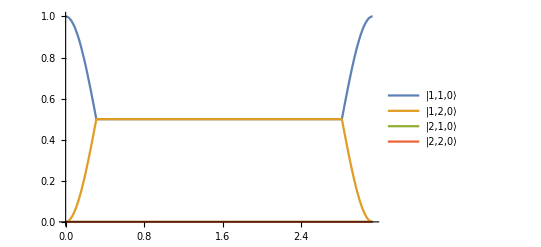

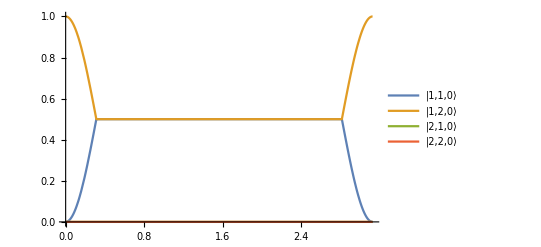

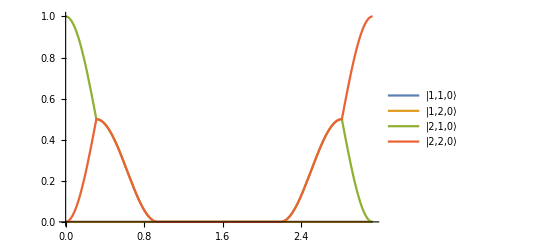

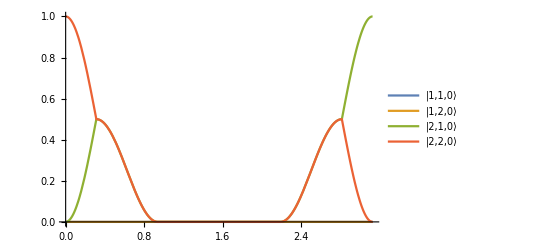

```mathematica
part=Part->{Addr[1,1,0],Addr[1,2,0],Addr[2,1,0],Addr[2,2,0]};
H=Hamiltonian@defs;
EvolutionPlot[H,1,1,0,t,part]
EvolutionPlot[H,1,2,0,t,part]
EvolutionPlot[H,2,1,0,t,part]
EvolutionPlot[H,2,2,0,t,part]
```

### MS Gate

```mathematica
TrappedIon[{2},{1,4}];
```

```mathematica
T=.;
defs={{{{1,{1,2,-1}},{0.01,0,δ}},{{1,{1,2,1}},{0.01,0,-δ}},{{2,{1,2,-1}},{0.01,0,δ}},{{2,{1,2,1}},{0.01,0,-δ}},T}}/.δ->0.1;
```

```mathematica
Frequency[n_,{1,2,-1}]:=231.3;
Frequency[n_,{1,2,1}]:=234.7;
Strength[1,{1,2,-1}]=0.5/30;
Strength[1,{1,2,1}]=0.5/35;
Strength[2,{1,2,-1}]=0.5/40;
Strength[2,{1,2,1}]=0.5/45;
```

```mathematica
Wave@defs
```

{{231.4,0,0.6,0,1,Null},{234.6,0,0.7,0,1,Null},{231.4,0,0.8,0,1,Null},{234.6,0,0.9,0,1,Null},{0,T,1,0,1,[0 1 2 3]}}

```mathematica
H=Hamiltonian[defs/.T->500];
Chop[Evolution[H,1,1,0]+2,2,0,1*^-3]
Chop[Evolution[H,1,2,0]+2,1,0,1*^-3]
Chop[Evolution[H,2,1,0]+1,2,0,1*^-3]
Chop[Evolution[H,2,2,0]+1,1,0,1*^-3]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

«1 more identical outputs»

(0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0
0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0
0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0
0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t)
0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0
0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0
0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0
0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t)
0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0
0 | 0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0.0314159 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0.0314159 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0.0444288 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0.054414 ⅇ^((0.-0.628319 ⅈ) t) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0.054414 ⅇ^((0.+0.628319 ⅈ) t) | 0 | 0 | 0 | 0 | 0)

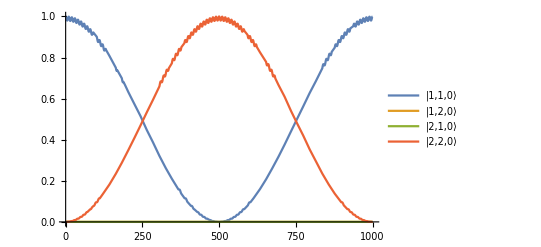

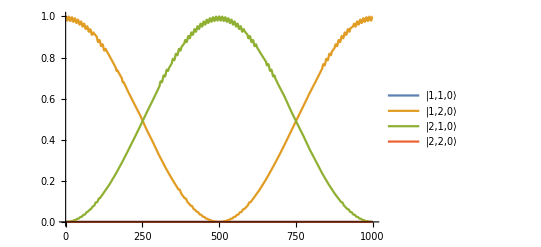

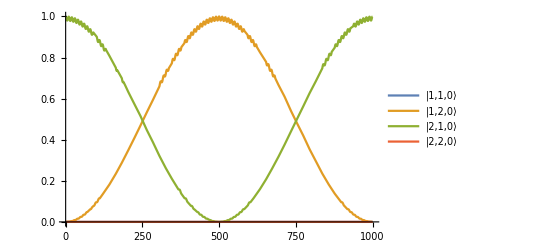

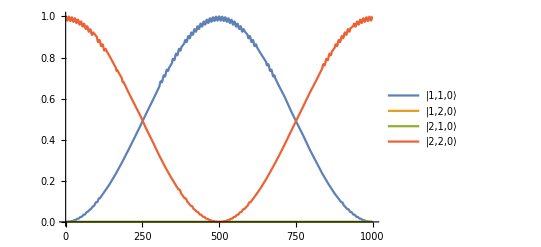

```mathematica
H=Hamiltonian[defs/.T->1000];
H⟦1,1,1⟧//MatrixForm
part=Part->{Addr[1,1,0],Addr[1,2,0],Addr[2,1,0],Addr[2,2,0]};
EvolutionPlot[H,1,1,0,t,part]
EvolutionPlot[H,1,2,0,t,part]
EvolutionPlot[H,2,1,0,t,part]
EvolutionPlot[H,2,2,0,t,part]
```

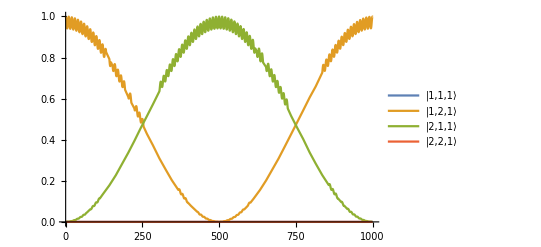
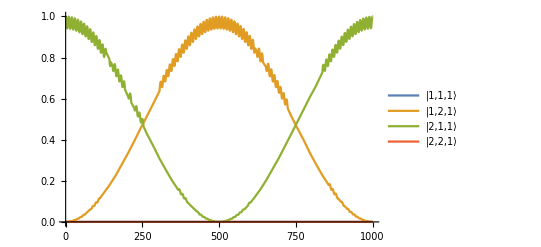
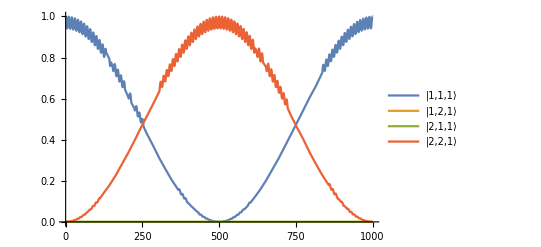
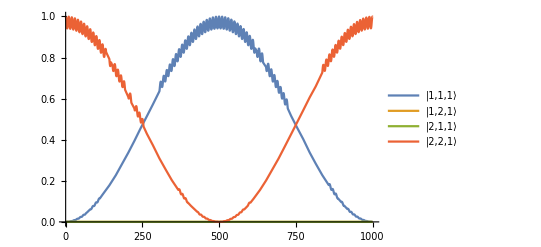
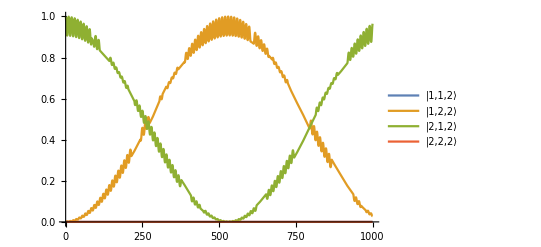
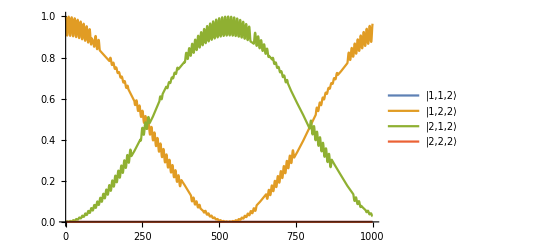
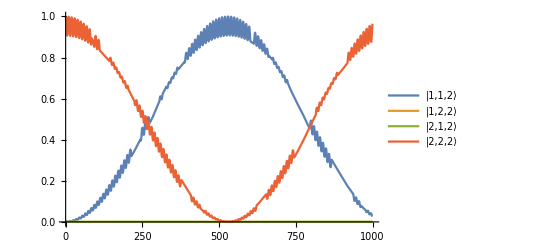
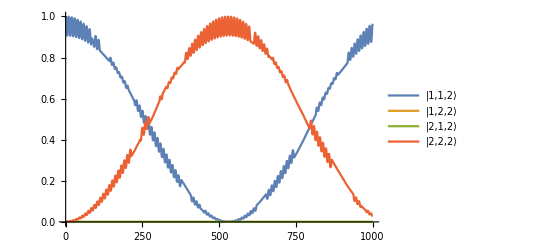
{-Graphics- -Graphics- -Graphics- -Graphics-,-Graphics- -Graphics- -Graphics- -Graphics-,-Graphics- -Graphics- -Graphics- -Graphics-}

```mathematica
H=Hamiltonian[defs/.T->1000];
Table[
part=Part->{Addr[1,1,k],Addr[1,2,k],Addr[2,1,k],Addr[2,2,k]};
EvolutionPlot[H,1,1,k,t,part]
EvolutionPlot[H,1,2,k,t,part]
EvolutionPlot[H,2,1,k,t,part]
EvolutionPlot[H,2,2,k,t,part],{k,0,2}]
```

```mathematica
photon count:3~15,2~9,0~1
```

```mathematica
{p^2,2p(1-p),(1-p)^2}/.p->Sin[t]^2
```

{Sin[t]^4,2 Sin[t]^2 (1-Sin[t]^2),(1-Sin[t]^2)^2}

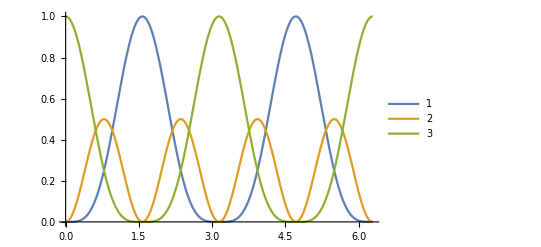

```mathematica
Plot[{Sin[t]^4,2 Sin[t]^2 (1-Sin[t]^2),(1-Sin[t]^2)^2},{t,0,2π},PlotLegends->Automatic]
```

(-π/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (3 π)/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 π)/10 | 0 | 0 | 0 | (3 π)/10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 π)/10 | 0 | 0 | 0 | (3 π)/10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -π/10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -π/10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 π)/10)

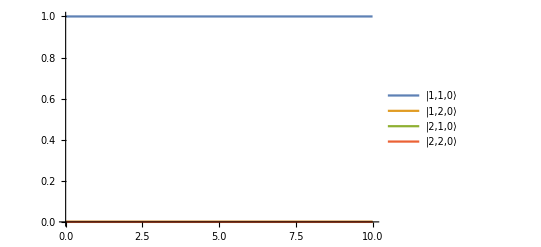

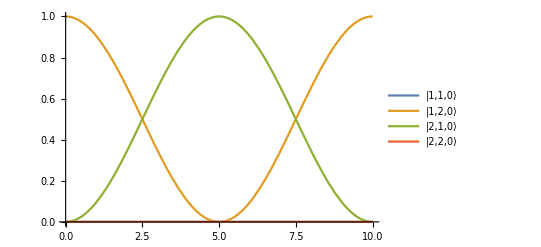

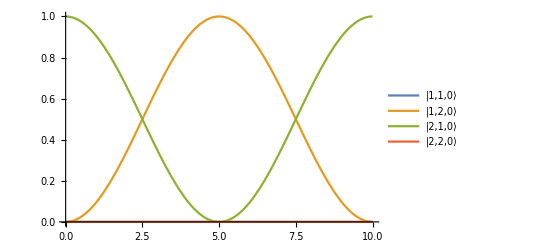

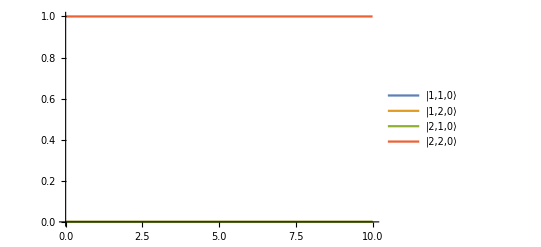

```mathematica
T=.;
defs={{{{1,{1,2,-1}},{1,0,δ}},{{1,{1,2,1}},{1,0,-δ}},{{2,{1,2,-1}},{1,0,δ}},{{2,{1,2,1}},{1,0,-δ}},T}}/.δ->10;
H=EffectiveHamiltonian@Hamiltonian[defs/.T->10];
H⟦1,1,1⟧//MatrixForm
part=Part->{Addr[1,1,0],Addr[1,2,0],Addr[2,1,0],Addr[2,2,0]};
EvolutionPlot[H,1,1,0,t,part,Method->Constant]
EvolutionPlot[H,1,2,0,t,part,Method->Constant]
EvolutionPlot[H,2,1,0,t,part,Method->Constant]
EvolutionPlot[H,2,2,0,t,part,Method->Constant]
```

### Real Field Coupling

```mathematica
ClearAll[Frequency,Strength];
Frequency@{args__}:=Frequency[args];
Strength@{args__}:=Strength[args];
Strength[__]=1;
```

```mathematica
TrappedIon[{1,4},{}];
```

```mathematica
Wave@{{Horn[1,2],{π,0}}}
```

{{Frequency[Horn[1,2]],1/2,1,0,1,Null}}

```mathematica
Hamiltonian@{{Horn[1,2],{π,0}}}
```

Piecewise[{{Hermitian[π Coupling[Horn[1,2]]], 0≤t≤1/2}, {0, True}}]

```mathematica
wave to defs
```

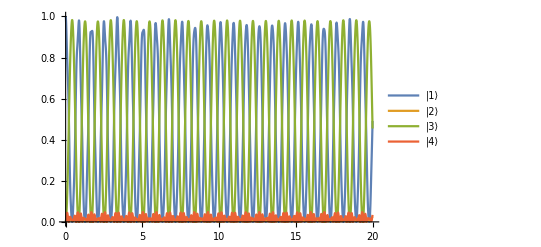

```mathematica
defs={{{{1,2},{0.9,0,f-195}},{{1,3},{1.2,0,f-200}},{{1,4},{1.1,0,f-205}},T}}/.{f->200,T->20};
EvolutionPlot[Hamiltonian@defs]
```

```mathematica
frequency scan/duration scan
```

```mathematica
Polarization,All Levels,Full Coupling Hamiltonian
```

```mathematica
AWG/DDS/Laser1/Laser2/.../Horn1/Horn2/...,Parallel,MergePiecewise
```

```mathematica
ClearAll[Push];
Push/:Coupling@Push:=Coupling[1,1,1]+2Coupling[2,2,1]+Coupling[3,3,1];
Push/:Frequency@Push=Frequency[2,2,1];
Push/:Strength@Push=Strength[2,2,1];

ClearAll[Qubit];
Qubit/:Coupling@Qubit[]:=Sum[ⅈ^(Abs@k) Omega[1,3,k]Coupling[1,3,k],{k,-1,1}];
Qubit/:Coupling@Qubit[k_]:= (*Coupling[1,3,k]*)Coupling@Qubit[]/Omega[1,3,k];
Qubit/:Frequency@Qubit[k_]:=Frequency[1,3,k];
Qubit/:Strength@Qubit[k_]:=Strength[1,3,k];
```

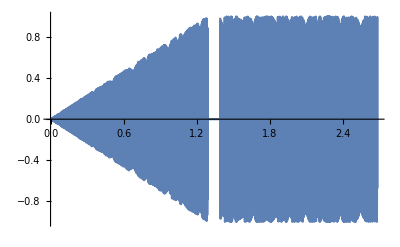

```mathematica
WavePlot@Each[{Horn[190.0587,1.292,1.,0,0.1,t/d Cos[w t]],Horn[190.0587,1.292,1.,1/2,0.1,Null]},List]
```

```mathematica
Include/@{"Data.nb","..\\LabVIEW\\LabVIEW.m","Sequence.nb"};
```

```mathematica
sequencer=GetAllCtrls@"E:\\LabVIEW\\Sequencer\\Sequencer.vi";
```

```mathematica
CtrlGetValue@sequencer["Sequence File"]
```

E:\Data\Sequence\Cooling.seq

```mathematica
CtrlSignalValue[sequencer["Sequence File"],"E:\\Data\\Sequence\\Pumping.seq"];
```

```mathematica
CtrlGetValue@*sequencer/@{"Item","Parameter","Start","End","Step"}
```

{Time,0,1.,1.,1.}

```mathematica
CtrlSignalValue[sequencer["Item"],"Time"];
```

```mathematica
Each[{{"Parameter",1},{"Start",0.1},{"End",10},{"Step",0.1}},CtrlSetValue[sequencer@#1,#2]&];
```

```mathematica
seq={Cooling[1000],Pumping[3],HornX[6.9],Detection[300,1,1],Zero[10]};
```

```mathematica
ExportSequenceString@seq
```

Chapter(Cooling,
00000000 00000000 00000000)
Chapter(Pumping,
10010000 00000000 00000000)
Chapter(HornX,
10000010 00000000 00000000)
Chapter(Detection,
10001000 00000000 00001111,
10001000 00000000 00000000,
10001000 00000000 00010000)
Chapter(Zero,
10000000 00000000 00000000)
----------
Cooling(1000)
Pumping(3)
HornX(6.9)
Detection(300,1,1)
Zero(10)

```mathematica
ExportSequencePacket@seq
```

{144,0,0,0,0,0,0,0,0,100,1000,3,6.9,300,1,1,10,64,0,0,0,0,38,0,0,0,0,64,0,0,0,0,38,0,0,0,0,64,0,0,0,0,38,0,0,0,0,64,0,0,0,0,38,0,0,0,0,64,0,0,0,0,38,0,0,0,0,64,252,0,0,0,29,0,0,0,0,64,0,0,0,0,39,0,0,0,0,96,0,0,0,0,38,0,0,0,0}

```mathematica
ClearAll[DDS];
DDS[id_Integer,key_String,val_:Null]:=(If[Quiet@Check[Socket`SocketInformation@$DDS,Null,Socket`SocketInformation::nosocket]===Null,Quiet@Close@$DDS;$DDS=SocketConnect[{"127.0.0.1",9999}]];If[val=!=Null,
WriteString[$DDS,key<>" "<>ToString@id<>" "<>ToString@val<>"\n"];,
WriteString[$DDS,key<>"? "<>ToString@id<>"\n"];
Pause[0.01];
ToExpression@StringTrim@ReadString[$DDS,EndOfBuffer]]);
```

```mathematica
DDS[5,#]&/@{"PROFILE","FREQ"}
```

{0,233.017}

```mathematica
DDS[5,"PROFILE",1]
```

```mathematica
DDS[5,"FREQ",233.019]
```

```mathematica
start=0;
end=100;
step=1;
now=0;
```

```mathematica
(*If[OptionValue@Plot,PrintTemporary@Dynamic@DataPlot[list,PlotLabels->ToString/@{exprs}]];*)
stop=False;
PrintTemporary@Button["●STOP",stop=True];
Monitor[(*Do[If[stop,Break[]];*)
While[stop=!=True&&end-now≥step,Pause[1];now+=step],(*Quiet@ListPlot[counts]*)ProgressIndicator[now,{start,end}]];
If[stop||end-now≥step,Abort[]];Print[now];
(*If[OptionValue@Plot,Print@list;Print@DataPlot[list,PlotLabels->ToString/@{exprs}]];*)
```

$Aborted